# Notebook for : Elementary Differential Geometry by Andrew Pressley

Geoff Cope
University of Utah
                                                                                                             𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
May 8, 2020

```mathematica
(* 
To do:  Serret Frenet Formulas 
Weingarten map page 139 
geodesic equations page 176
Codzaai Mainardi Equations page 240 
*)
```

```mathematica
(* 
find unit speed definition and put at top 
*)
```

```mathematica
(*
Add dtReplace 
*)
```

```mathematica
(* 
See solutions in back 
*)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book

```mathematica
Hyperlink["Elementary Differential Geometry by Andrew Pressley",
"https://link.springer.com/book/10.1007/978-1-84882-891-9"]
```

[Elementary Differential Geometry by Andrew Pressley](https://link.springer.com/book/10.1007/978-1-84882-891-9)

```mathematica
Hyperlink["Elementary Differential Geometry by Andrew Pressley PDF",
"http://dwwebs.com/combinedpdf.pdf"]
```

[Elementary Differential Geometry by Andrew Pressley PDF](http://dwwebs.com/combinedpdf.pdf)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 3291 Kb

{Utilities`CleanSlate`,Notation`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"]
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[w]-> dw , 
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv ,
Dt[x]-> dx , 
Dt[y]-> dy , 
Dt[z]-> dz ,  
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[φ] -> dφ , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓏] -> d𝓏,
Dt[T]-> dT , 
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ};
dtReplace // TableForm
```

Dt[w]→dw
Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[φ]→dφ
Dt[𝓉]→d𝓉
Dt[𝓏]→d𝓏
Dt[T]→dT
Dt[U]→dU
Dt[V]→dV
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ

```mathematica
M /: Dt[M] = 0 ;  (* Mass of Schwarzschild is constant as example *)
```

## Line Element and Metric Functions (Fix a few of these)

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

```mathematica
Clear[magnitude]
magnitude[V_]:= 
Sqrt[Sum[V[[i]]^2, { i,1, Length[V] }]] // Expand // Simplify // PowerExpand
```

```mathematica
(* Definition appears Page 25 Equation 1  *) 
Clear[curvature]
curvature[γ_,t_] := 
magnitude[Cross[ D[γ[t], {t,2}] , D[γ[t], t] ]]/magnitude[ D[γ[t], t] ]^3// PowerExpand
```

```mathematica
(* Definition appears Page 38 Equation 11  *) 
Clear[torsion]
torsion[γ_,t_] := 
(Cross[ D[γ, t] ,  D[γ, {θ,2}] ] . D[γ, {t,3}])/(Cross[ D[γ, t] ,  D[γ, {t,2}] ] . Cross[ D[γ, t] ,  D[γ, {t,2}] ]) // Expand // Simplify
```

```mathematica
(*  First Fundamental Form *) 
(* Definition appears Page 98 Equation 2  *) 
Clear[fff]
fff[σ_,u_,v_,du_,dv_] := 
Simplify[Expand[D[σ, u] . D[σ, u]] ] du^2 +  2 Simplify[Expand[D[σ, u] . D[σ, v]] ]  du dv + Simplify[Expand[D[σ, v] . D[σ, v]] ] dv^2
```

```mathematica
(* Definition appears Page 75 Equation 3  *) 
Clear[normalN]
normalN[σ_,u_,v_] := 
Simplify[Cross[ D[σ, u] , D[σ, v] ]]/PowerExpand[Sqrt[Simplify[Expand[Cross[ D[σ, u] , D[σ, v] ]  . Cross[ D[σ, u] , D[σ, v] ]]] ]]
```

```mathematica
(* Second Fundamental Form *) 
(* Definition appears Page 125 Equation 4  *) 
Clear[sff]
sff[σ_,u_,v_,du_,dv_] := 
( D[D[σ, u], u] . normalN[σ,u,v] ) du^2 + 2 ( D[D[σ, v], u]  . normalN[σ,u,v] ) du dv + ( D[D[σ, v], v]  . normalN[σ,u,v] ) dv^2 // Simplify
```

```mathematica
(* Definition appears top of Page 98  *) 
(* Definition appears Page 104  *) 
Clear[ℰ]
ℰ[σ_,u_,v_] :=  
Simplify[ D[σ, u] . D[σ, u]  ]
```

```mathematica
(* Definition appears top of Page 98  *) 
(* Definition appears Page 104  *) 
Clear[F]
F[σ_,u_,v_] :=
 Simplify[ D[σ, u] . D[σ, v]  ]
```

```mathematica
(* Definition appears top of Page 98  *) 
(* Definition appears Page 104  *) 
Clear[G]
G[σ_,u_,v_] := 
 Simplify[ D[σ, v] . D[σ, v] ]
```

```mathematica
(* Definition appears Page 113  *) 
Clear[areaIntegrand]
areaIntegrand[σ_,u_,v_] := 
PowerExpand[Sqrt[Simplify[Expand[Cross[ D[σ, u] , D[σ, v] ]  . Cross[ D[σ, u] , D[σ, v] ]]]]]
```

```mathematica
(* Definition appears Page 124 Equation 3 *) 
Clear[L]
L[σ_,u_,v_] := 
 Simplify[ D[D[σ, u], u] . normalN[σ,u,v] ]
```

```mathematica
(* Definition appears Page 124 Equation 3 *) 
Clear[M]
M[σ_,u_,v_] := 
Simplify[ D[D[σ, v], u] . normalN[σ,u,v] ]
```

```mathematica
(* Definition appears Page 124 Equation 3 *) 
(* Relationship Between Gaussin Curvature K and N given on page 167 *) 
Clear[𝒩] (* here we use [esc]scN[esc] for 𝒩 instead of N which is reserved *) 
𝒩[σ_,u_,v_] := 
Simplify[ D[D[σ, v], v] . normalN[σ,u,v] ]
```

```mathematica
(* Definition appears Page 132 Equation 12 *) 
Clear[det]
det[σ_,u_,v_] := 
 ({{L[σ,u,v] - κ  ℰ[σ,u,v], M[σ,u,v] - κ F[σ,u,v]}, {M[σ,u,v] - κ  F[σ,u,v], 𝒩[σ,u,v] - κ G[σ,u,v]}}) ;
```

```mathematica
Clear[solution]
solution[σ_,u_,v_] := 
Simplify[Solve[ Det[det[σ,u,v]] == 0 , κ ]]
```

```mathematica
Clear[κ1,κ1replace ]
κ1replace[σ_,u_,v_] := 
solution[σ,u,v][[1]] /. { κ-> κ1}
```

```mathematica
Clear[κ2,κ2replace ]
κ2replace[σ_,u_,v_] := 
solution[σ,u,v][[2]] /. { κ-> κ2}
```

```mathematica
(* Definition appears Page 147 *) 
(* Relationship Between Gaussin Curvature K and N given on page 167 *) 
Clear[gaussianCurvatureK]
gaussianCurvatureK[σ_,u_,v_] := 
 ( κ1 κ2 ) /. κ1replace[σ,u,v] /. κ2replace[σ,u,v]  // Expand // Simplify ;
```

```mathematica
(* Definition appears Page 147 *) 
Clear[meanCurvatureH]
meanCurvatureH[σ_,u_,v_] := 
 1/2( κ1 + κ2 ) /. κ1replace[σ,u,v] /. κ2replace[σ,u,v]  // Expand // Simplify ;
```

## Problem 1.7 Page 6

```mathematica
Clear[problem1pt7]
problem1pt7 = 
γ ==(  a { t - Sin[t], 1 - Cos[t] }  ) /. a-> 1
```

γ=={t-Sin[t],1-Cos[t]}

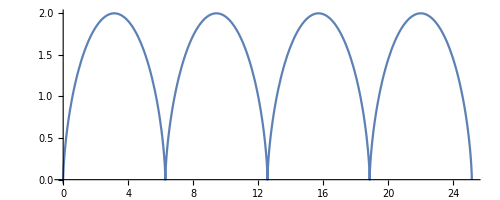

```mathematica
ParametricPlot[ problem1pt7[[2]], {t,0,8 π}]
```

## Problem 1.9 Page 6

```mathematica
Clear[problem1pt9]
problem1pt9 = 
γ ==  { Cos[t]^2-1/2, Sin[t] Cos[t], Sin[t] }
```

γ=={-1/2+Cos[t]^2,Cos[t] Sin[t],Sin[t]}

```mathematica
Manipulate[ParametricPlot3D[problem1pt9[[2]], {t,0,tmax}] ,{ tmax , 0.1 , 10 } ]
```

## Problem 1.10 Page 7

```mathematica
Clear[problem1pt10] (* 1/100 put in just for plotting purposes *) 
problem1pt10 = 
γ ==(  {Exp[a t] Cos[t] , Exp[a t] Sin[ t]} /. a-> 1/100 )
```

γ=={ⅇ^(t/100) Cos[t],ⅇ^(t/100) Sin[t]}

```mathematica
Manipulate[ParametricPlot[problem1pt10[[2]], {t,0,tmax}] ,{ tmax , 0.1 , 300 } ]
```

## Example 1.4 Page 8

```mathematica
Clear[example1pt4]
example1pt4 = 
γ ==  {Exp[ t] Cos[t] , Exp[ t] Sin[ t]}
```

γ=={ⅇ^t Cos[t],ⅇ^t Sin[t]}

```mathematica
D[example1pt4[[2]], t]
```

{ⅇ^t Cos[t]-ⅇ^t Sin[t],ⅇ^t Cos[t]+ⅇ^t Sin[t]}

```mathematica
D[example1pt4[[2]], t] . D[example1pt4[[2]], t]
```

(ⅇ^t Cos[t]-ⅇ^t Sin[t])^2+(ⅇ^t Cos[t]+ⅇ^t Sin[t])^2

```mathematica
D[example1pt4[[2]], t] . D[example1pt4[[2]], t]  // Expand // Simplify
```

2 ⅇ^(2 t)

```mathematica
Integrate[ (( √(D[example1pt4[[2]], t] . D[example1pt4[[2]], t])    // Expand // Simplify   ) /. t-> u  ) , {u,0,t} ]
```

ConditionalExpression[√2 (-1+√(ⅇ^(2 t))), ⅇ^(2 t)≥0]

## Exercise 1.11 Page 9

```mathematica
Clear[exercise1pt11]
exercise1pt11 = 
γ == {t,Cosh[t]}
```

γ=={t,Cosh[t]}

```mathematica
D[exercise1pt11[[2]], t] . D[exercise1pt11[[2]], t]
```

1+Sinh[t]^2

```mathematica
( √(D[exercise1pt11[[2]], t] . D[exercise1pt11[[2]], t])  /. t-> u  )
```

√(1+Sinh[u]^2)

```mathematica
∫_0^t ( √(D[exercise1pt11[[2]], t] . D[exercise1pt11[[2]], t])  /. t-> u  ) ⅆu
```

ConditionalExpression[√(Cosh[t]^2) Tanh[t], 0<Im[t]<π/2||-π/2<Im[t]<0||Re[t]≠0]

## Example 1.7 Page 14

```mathematica
Clear[example1pt7]
example1pt7 = 
γ ==  { t, t^2, t^3 }
```

γ=={t,t^2,t^3}

```mathematica
D[example1pt7[[2]], t]
```

{1,2 t,3 t^2}

```mathematica
√(D[example1pt7[[2]], t] . D[example1pt7[[2]], t])
```

√(1+4 t^2+9 t^4)

```mathematica
∫_0^t (√(D[example1pt7[[2]], t] . D[example1pt7[[2]], t]) /. t-> u ) ⅆu
```

∫_0^t √(1+4 u^2+9 u^4)ⅆu

```mathematica
Manipulate[ParametricPlot3D[example1pt7[[2]], {t,0,tmax}] ,{ tmax , 0.1 , 10 } ]
```

## Definition 2.1 Page 24

```mathematica
Clear[definition2pt1]
definition2pt1 = 
γ  ==  { x0 + R Cos[s/R] , y0 + R Sin[s/R] }
```

γ=={x0+R Cos[s/R],y0+R Sin[s/R]}

```mathematica
D[definition2pt1[[2]], s]
```

{-Sin[s/R],Cos[s/R]}

```mathematica
D[definition2pt1[[2]], s] . D[definition2pt1[[2]], s]
```

Cos[s/R]^2+Sin[s/R]^2

```mathematica
D[definition2pt1[[2]], s] . D[definition2pt1[[2]], s]  // Simplify
```

1

```mathematica
D[definition2pt1[[2]], {s,2}]
```

{-Cos[s/R]/R,-Sin[s/R]/R}

```mathematica
D[definition2pt1[[2]], {s,2}] . D[definition2pt1[[2]], {s,2}]
```

Cos[s/R]^2/R^2+Sin[s/R]^2/R^2

```mathematica
D[definition2pt1[[2]], {s,2}] . D[definition2pt1[[2]], {s,2}]  // Simplify
```

1/R^2

## Example 2.1

```mathematica
Clear[example2pt1]
example2pt1 = 
γ[θ]  ==   { a Cos[θ], a Sin[θ] , b θ }
```

γ[θ]=={a Cos[θ],a Sin[θ],b θ}

```mathematica
D[example2pt1[[2]], θ]
```

{-a Sin[θ],a Cos[θ],b}

```mathematica
D[example2pt1[[2]], θ] . D[example2pt1[[2]], θ]
```

b^2+a^2 Cos[θ]^2+a^2 Sin[θ]^2

```mathematica
D[example2pt1[[2]], θ] . D[example2pt1[[2]], θ]  // Simplify
```

a^2+b^2

```mathematica
√(D[example2pt1[[2]], θ] . D[example2pt1[[2]], θ]) // Simplify
```

√(a^2+b^2)

```mathematica
D[example2pt1[[2]], {θ,2}]
```

{-a Cos[θ],-a Sin[θ],0}

```mathematica
Cross[ D[example2pt1[[2]], {θ,2}] , D[example2pt1[[2]], θ] ]
```

{-a b Sin[θ],a b Cos[θ],-a^2 Cos[θ]^2-a^2 Sin[θ]^2}

```mathematica
magnitude[Cross[ D[example2pt1[[2]], {θ,2}] , D[example2pt1[[2]], θ] ]]
```

a √(a^2+b^2)

```mathematica
magnitude[D[example2pt1[[2]], θ]]
```

√(a^2+b^2)

```mathematica
κ == magnitude[Cross[ D[example2pt1[[2]], {θ,2}] , D[example2pt1[[2]], θ] ]]/(magnitude[D[example2pt1[[2]], θ]])^3
```

κ==a/(a^2+b^2)

## Example 2.4 Page 39

```mathematica
Clear[example2pt4]
example2pt4 = 
γ  ==  { a Cos[θ] , a  Sin[θ], b θ }
```

γ=={a Cos[θ],a Sin[θ],b θ}

```mathematica
D[example2pt4[[2]], θ]
```

{-a Sin[θ],a Cos[θ],b}

```mathematica
D[example2pt4[[2]], {θ,2}]
```

{-a Cos[θ],-a Sin[θ],0}

```mathematica
D[example2pt4[[2]], {θ,3}]
```

{a Sin[θ],-a Cos[θ],0}

```mathematica
(Cross[D[example2pt4[[2]], θ], D[example2pt4[[2]], {θ,2}]] . D[example2pt4[[2]], {θ,3}])/(Cross[D[example2pt4[[2]], θ], D[example2pt4[[2]], {θ,2}]] . Cross[D[example2pt4[[2]], θ], D[example2pt4[[2]], {θ,2}]]) // Expand // Simplify
```

b/(a^2+b^2)

## Example 4.2 Page 61 Sphere

```mathematica
Clear[example4pt2]
example4pt2 = 
S2 ==  x^2+y^2+z^2== 1
```

S2==x^2+y^2+z^2==1

```mathematica
example4pt2[[2;;3]]
```

x^2+y^2+z^2==1

```mathematica
ContourPlot3D[Evaluate[example4pt2[[2;;3]]] , { x,-1.1,1.1},{y,-1.1,1.1},{z,-1.1,1.1}]
```

-Graphics3D-

```mathematica
Clear[example4pt2b]
example4pt2b = 
σ  ==  { Cos[θ] Cos[ϕ], Cos[θ] Sin[ϕ], Sin[θ] }
```

σ=={Cos[θ] Cos[ϕ],Cos[θ] Sin[ϕ],Sin[θ]}

```mathematica
example4pt2b[[2]]
```

{Cos[θ] Cos[ϕ],Cos[θ] Sin[ϕ],Sin[θ]}

```mathematica
Manipulate[
ParametricPlot3D[Evaluate[ example4pt2b[[2]] ]  ,{θ,-θf, θf}, {ϕ,- ϕf,ϕf},  PlotRange-> { {-1,1}, {-1,1}, {-1,1} }  ] ,
{θf,0.1,π/2},{ϕf,0.1,π} ]
```

```mathematica
Manipulate[
ParametricPlot3D[ {  a Cos[θ] Cos[ϕ], b Cos[θ] Sin[ϕ],c  Sin[θ] } , { ϕ,-ϕf, ϕf } , { θ, -θf, θf },  PlotRange-> { {-1,1}, {-1,1}, {-1,1} } ] ,
{ a, 0.1, 1 },
{b,0.1,1},
{c,0.1,1},
{θf, 0.1, π/2} ,
{ ϕf, 0.1, π } 
]
```

```mathematica
fff[example4pt2b[[2]],θ,ϕ,dθ,dϕ]
```

dθ^2+dϕ^2 Cos[θ]^2

```mathematica
lineToMetric[ fff[example4pt2b[[2]],θ,ϕ,dθ,dϕ] , {dθ,dϕ} ]  // MatrixForm
```

(1 | 0
0 | Cos[θ]^2)

```mathematica
Collect[ TrigExpand[sff[example4pt2b[[2]],θ,ϕ,dθ,dϕ]] , {dθ^2,dϕ^2} ]
```

dθ^2+dϕ^2 (1/2+Cos[θ]^2/2-Sin[θ]^2/2)

```mathematica
lineToMetric[ sff[example4pt2b[[2]],θ,ϕ,dθ,dϕ] , {dθ,dϕ} ] // TrigExpand   // Simplify // MatrixForm
```

(1 | 0
0 | Cos[θ]^2)

```mathematica
gaussianCurvatureK[example4pt2b[[2]],θ,ϕ ]
```

1

```mathematica
meanCurvatureH[example4pt2b[[2]],θ,ϕ]
```

1

## Example 4.3 Page 63 Double Cone (Only Upper Plotted)

```mathematica
Clear[example4pt3]
example4pt3= 
S ==  x^2+y^2== z^2
```

S==x^2+y^2==z^2

```mathematica
example4pt3[[2;;3]]
```

x^2+y^2==z^2

```mathematica
ContourPlot3D[Evaluate[example4pt3[[2;;3]]] , { x,-1.1,1.1},{y,-1.1,1.1},{z,-1.1,1.1}]
```

-Graphics3D-

```mathematica
(*  We just plot the upper half *) 
Clear[example4pt3b]
example4pt3b = 
σ  ==  { u,v,√(u^2+v^2) }
```

σ=={u,v,√(u^2+v^2)}

```mathematica
example4pt3b[[2]]
```

{u,v,√(u^2+v^2)}

```mathematica
Manipulate[
ParametricPlot3D[Evaluate[ example4pt3b[[2]] ]  ,{u,-uf,uf}, {v,-vf,vf},  PlotRange-> { {-3,3}, {-3,3}, {-1,4} }  ] ,
{uf,0.1,4},{vf,0.1,4} ]
```

```mathematica
gaussianCurvatureK[example4pt3b[[2]],u,v]
```

0

```mathematica
meanCurvatureH[example4pt3b[[2]],u,v]
```

1/(2 √2 √(u^2+v^2))

## Exercise 4.4 Page 66 Hyperboloid of One Sheet

```mathematica
Clear[exercise4pt4a]
exercise4pt4a=
S == x^2+ y^2-z^2== 1  ;
exercise4pt4a[[2;;3]]
```

x^2+y^2-z^2==1

```mathematica
ContourPlot3D[x^2+ y^2-z^2== 1  , {x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-

```mathematica
Clear[exercise4pt4b]
exercise4pt4b= { 
(x-z) Cos[θ] == (1-y) Sin[θ] , 
(x+z) Sin[θ] == (1+y) Cos[θ]
} ;
exercise4pt4b // TableForm
```

(x-z) Cos[θ]==(1-y) Sin[θ]
(x+z) Sin[θ]==(1+y) Cos[θ]

```mathematica
Flatten[Solve[exercise4pt4b , {x,z} ]] // TableForm
```

x→Tan[θ]
z→y Tan[θ]

```mathematica
(*  Shows the line is contained in S *) 
exercise4pt4a[[2;;3]]
exercise4pt4a[[2;;3]] /. Flatten[Solve[exercise4pt4b , {x,z} ]] // Expand // FullSimplify
```

x^2+y^2-z^2==1

True

## Example 4.7 Page 71

```mathematica
Clear[example4pt7]
example4pt7 = 
f  ==  x^2+y^2+z^2-1 == 0
```

f==-1+x^2+y^2+z^2==0

```mathematica
Grad[ example4pt7[[2]] , {x,y,z} ]
```

{2 x,2 y,2 z}

```mathematica
Grad[ example4pt7[[2]] , {x,y,z} ]  . Grad[ example4pt7[[2]] , {x,y,z} ]
```

4 x^2+4 y^2+4 z^2

```mathematica
√(Grad[ example4pt7[[2]] , {x,y,z} ]  . Grad[ example4pt7[[2]] , {x,y,z} ])
```

√(4 x^2+4 y^2+4 z^2)

```mathematica
Flatten[Solve[ example4pt7[[2;;3]] , x ] ][[2]]
```

x→√(1-y^2-z^2)

```mathematica
√(Grad[ example4pt7[[2]] , {x,y,z} ]  . Grad[ example4pt7[[2]] , {x,y,z} ])  /. Flatten[Solve[ example4pt7[[2;;3]] , x ] ][[2]] // Expand // Simplify
```

2

## Exercise 4.8 Page 72

```mathematica
Clear[exercise4pt8]
exercise4pt8 = 
σ == { r Cosh[θ] , r Sinh[θ] , r^2 }
```

σ=={r Cosh[θ],r Sinh[θ],r^2}

```mathematica
Manipulate[ParametricPlot3D[{ r Cosh[θ] , r Sinh[θ] , r^2 } , { r, 0, rf } , { θ, 0, θf} ] ,{rf, 0.1, 3 },{θf, 0.1,  3 } ]
```

## Exercise 4.9 Page 73 (Add Calculations From Earlier notebook)

```mathematica
Clear[exercise4pt9]
exercise4pt9 = 
(x/a)^2+(y/b)^2+(z/c)^2== 1
```

x^2/a^2+y^2/b^2+z^2/c^2==1

```mathematica
Manipulate[ContourPlot3D[ (x/a)^2+(y/b)^2+(z/c)^2== 1 , { x, -a-1, a+1}, {y, -b-1,b+1}, { z, -c - 1,c+1  } ] ,
{a,1,4},
{b,1,4},
{c,1,4}]
```

```mathematica
Grad[ exercise4pt9[[1]] , {x,y,z} ]
```

{(2 x)/a^2,(2 y)/b^2,(2 z)/c^2}

```mathematica
Grad[ exercise4pt9[[1]] , {x,y,z} ]  . Grad[ exercise4pt9[[1]] , {x,y,z} ]
```

(4 x^2)/a^4+(4 y^2)/b^4+(4 z^2)/c^4

```mathematica
√(Grad[ exercise4pt9[[1]] , {x,y,z} ]  . Grad[ exercise4pt9[[1]] , {x,y,z} ])
```

√((4 x^2)/a^4+(4 y^2)/b^4+(4 z^2)/c^4)

```mathematica
Flatten[Solve[ exercise4pt9 , x ] ][[2]]
```

x→(a √(b^2 c^2-c^2 y^2-b^2 z^2))/(b c)

```mathematica
√(Grad[ exercise4pt9[[1]] , {x,y,z} ]  . Grad[ exercise4pt9[[1]] , {x,y,z} ]) /. Flatten[Solve[ exercise4pt9 , x ] ][[2]] // Expand // FullSimplify
```

2 √(y^2/b^4+z^2/c^4-(-1+y^2/b^2+z^2/c^2)/a^2)

## Exercise 4.10 Page 73 (Partially done)(Add Calculations From Earlier notebook)

```mathematica
Clear[exercise4pt10a]
exercise4pt10a =  
σ ==  { (  a + b Cos[θ] ) Cos[ϕ] , ( a + b Cos[θ] ) Sin[ϕ] , b Sin[θ] }
```

σ=={(a+b Cos[θ]) Cos[ϕ],(a+b Cos[θ]) Sin[ϕ],b Sin[θ]}

```mathematica
Manipulate[ParametricPlot3D[ { (  a + b Cos[θ] ) Cos[ϕ] , ( a + b Cos[θ] ) Sin[ϕ] , b Sin[θ] } ,{ θ, 0, θf} , { ϕ, 0 , ϕf} ] ,{a, 0.1, 3 } , { b, 0.1, 3 }, 
{ θf, 0.1, 2 π } , { ϕf, 0.1, 2 π }]
```

```mathematica
Clear[exercise4pt10b]
exercise4pt10b =  
σ == ( x^2+y^2+z^2+a^2-b^2)^2 == 4 a^2 ( x^2+y^2 )
```

σ==(a^2-b^2+x^2+y^2+z^2)^2==4 a^2 (x^2+y^2)

```mathematica
Manipulate[ContourPlot3D[( x^2+y^2+z^2+a^2-b^2)^2 == 4 a^2 ( x^2+y^2 ) , {x,-3,3},{y,-3,3},{z,-3,3}],{a,0,2},{b,0,2}]
```

## Example 4.9 Page 76 (Add Calculations From Earlier notebook)

```mathematica
Clear[example4pt9]
example4pt9 = 
σ  ==  { ( 1 - u Sin[v/2]) Cos[v] , ( 1 - u Sin[v/2] ) Sin[v] , u Cos[v/2] }
```

σ=={Cos[v] (1-u Sin[v/2]),(1-u Sin[v/2]) Sin[v],u Cos[v/2]}

```mathematica
Evaluate[example4pt9[[2]]]
```

{Cos[v] (1-u Sin[v/2]),(1-u Sin[v/2]) Sin[v],u Cos[v/2]}

```mathematica
Manipulate[ParametricPlot3D[ Evaluate[example4pt9[[2]]], { u, -uf,uf} , { v, -vf , vf } ] ,{ uf, 0.1, 1 },{ vf, 0.1, π } ]
```

## Exercise 4.13 Page 77

```mathematica
Clear[exercise4pt13]
exercise4pt13 = 
σ  ==  { u Cosh[v], u Sinh[v], u^2 }
```

σ=={u Cosh[v],u Sinh[v],u^2}

```mathematica
Manipulate[ParametricPlot3D[ exercise4pt13[[2]], { u, -uf, uf} , { v, -vf, vf } ] ,{ uf, 0.1, 5 },{vf, 0.1, 5 }  ]
```

```mathematica
Clear[fff]
fff[σ_,u_,v_,du_,dv_] := 
Simplify[Expand[D[σ, u] . D[σ, u]] ] du^2 +  2 Simplify[Expand[D[σ, u] . D[σ, v]] ]  du dv + Simplify[Expand[D[σ, v] . D[σ, v]] ] dv^2
```

```mathematica
fff[exercise4pt13[[2]],u,v,du,dv]
```

dv^2 u^2 Cosh[2 v]+du^2 (4 u^2+Cosh[2 v])+2 du dv u Sinh[2 v]

```mathematica
lineToMetric[fff[exercise4pt13[[2]],u,v,du,dv] , {du,dv} ] // MatrixForm
```

(4 u^2+Cosh[2 v] | u Sinh[2 v]
u Sinh[2 v] | u^2 Cosh[2 v])

## Exercise 4.19 Page 83 (Add Calculations From Earlier notebook)

```mathematica
Clear[exercise4pt19]
exercise4pt19 = 
σ == { Sech[u] Cos[v], Sech[u] Sin[v], Tanh[u] }
```

σ=={Cos[v] Sech[u],Sech[u] Sin[v],Tanh[u]}

```mathematica
Manipulate[ParametricPlot3D[{ Sech[u] Cos[v], Sech[u] Sin[v], Tanh[u] }  , { u, -uf , uf } , { v, -vf , vf } ] ,{uf, 0.1, π  } , { vf, 0.1, π  } ]
```

```mathematica
fff[exercise4pt19[[2]],u,v,du,dv]
```

du^2 Sech[u]^2+dv^2 Sech[u]^2

```mathematica
lineToMetric[fff[exercise4pt19[[2]],u,v,du,dv] , {du,dv} ] // MatrixForm
```

(Sech[u]^2 | 0
0 | Sech[u]^2)

## Definition 4.6 Page 84

```mathematica
Clear[A]
A = 
({{a1, a4, a6}, {a4, a2, a5}, {a6, a5, a3}});
A // MatrixForm
```

(a1 | a4 | a6
a4 | a2 | a5
a6 | a5 | a3)

```mathematica
Clear[b]
b =
{ b1, b2, b3 } ;
b // MatrixForm
```

(b1
b2
b3)

```mathematica
Clear[r]
r = 
{ x, y, z } ;
r // MatrixForm
```

(x
y
z)

```mathematica
Clear[quadric]
quadric = 
r. ( A . r ) + b . r + c // Expand // Simplify  ;
quadric // TraditionalForm
```

a1 x^2+a2 y^2+a3 z^2+2 a4 x y+2 a5 y z+2 a6 x z+b1 x+b2 y+b3 z+c

```mathematica
Clear[A,b,r]
```

## Proposition 4.6 Page 85

```mathematica
Clear[proposition4pt6i]
proposition4pt6i = 
(x/p)^2+ (y/q)^2+ (z/r)^2 == 1
```

x^2/p^2+y^2/q^2+z^2/r^2==1

```mathematica
Manipulate[ContourPlot3D[(x/p)^2+ (y/q)^2+ (z/r)^2 == 1  , {x,-3,3},{y,-3,3},{z,-3,3}],{p,0.1,2.9},{q,0.1,2.9},{r,0.1,2.9}]
```

```mathematica
Clear[proposition4pt6ii]
proposition4pt6ii = 
(x/p)^2+ (y/q)^2-(z/r)^2 == 1
```

x^2/p^2+y^2/q^2-z^2/r^2==1

```mathematica
Manipulate[ContourPlot3D[(x/p)^2+ (y/q)^2- (z/r)^2 == 1  , {x,-3,3},{y,-3,3},{z,-3,3}],{p,0.1,2.9},{q,0.1,2.9},{r,0.1,2.9}]
```

```mathematica
Clear[proposition4pt6iii]
proposition4pt6iii = 
(z/r)^2-(x/p)^2-  (y/q)^2 == 1
```

-x^2/p^2-y^2/q^2+z^2/r^2==1

```mathematica
Manipulate[ContourPlot3D[(z/r)^2-(x/p)^2-  (y/q)^2 == 1   , {x,-3,3},{y,-3,3},{z,-3,3}],{p,0.1,2.9},{q,0.1,2.9},{r,0.1,2.9}]
```

```mathematica
Clear[proposition4pt6iv]
proposition4pt6iv = 
(x/p)^2+ (y/q)^2 == z
```

x^2/p^2+y^2/q^2==z

```mathematica
Manipulate[ContourPlot3D[(x/p)^2+ (y/q)^2 == z    , {x,-6,6},{y,-6,6},{z,0,3}],{p,0.1,2.9},{q,0.1,2.9}]
```

```mathematica
Clear[proposition4pt6v]
proposition4pt6v = 
(x/p)^2- (y/q)^2 == z
```

x^2/p^2-y^2/q^2==z

```mathematica
Manipulate[ContourPlot3D[(x/p)^2- (y/q)^2 == z    , {x,-6,6},{y,-6,6},{z,-3,3}],{p,0.1,2.9},{q,0.1,2.9}]
```

```mathematica
Clear[proposition4pt6vi]
proposition4pt6vi = 
(x/p)^2+ (y/q)^2- (z/r)^2 ==0
```

x^2/p^2+y^2/q^2-z^2/r^2==0

```mathematica
Manipulate[ContourPlot3D[(x/p)^2+ (y/q)^2- (z/r)^2 ==0   , {x,-3,3},{y,-3,3},{z,-3,3}],{p,0.1,2.9},{q,0.1,2.9},{r,0.1,2.9}]
```

```mathematica
Clear[proposition4pt6vii]
proposition4pt6vii = 
(x/p)^2+ (y/q)^2 == 1
```

x^2/p^2+y^2/q^2==1

```mathematica
Manipulate[ContourPlot3D[(x/p)^2+ (y/q)^2 == 1    , {x,-3,3},{y,-3,3},{z,-3,3}],{p,0.1,2.9},{q,0.1,2.9}]
```

```mathematica
Clear[proposition4pt6viii]
proposition4pt6viii = 
(x/p)^2- (y/q)^2 == 1
```

x^2/p^2-y^2/q^2==1

```mathematica
Manipulate[ContourPlot3D[(x/p)^2- (y/q)^2 == 1    , {x,-3,3},{y,-3,3},{z,-3,3}],{p,0.1,2.9},{q,0.1,2.9}]
```

```mathematica
Clear[proposition4pt6ix]
proposition4pt6ix = 
(x/p)^2 ==  y
```

x^2/p^2==y

```mathematica
Manipulate[ContourPlot3D[(x/p)^2 ==  y     , {x,-3,3},{y,0,3},{z,-3,3}],{p,0.1,2.9}]
```

## Section 4.6 Triply Orthogonal Systems

```mathematica
Clear[section4pt6]
section4pt6
```

section4pt6

```mathematica
Clear[F]
F[t_]:= x^2/(p^2-t)+ y^2/(q^2-t)+z^2/(r^2-t)
```

## Exercise 5.1 Page 100

```mathematica
Clear[exercise5pt1i]
exercise5pt1i = 
σ ==  { Sinh[u] Sinh[v], Sinh[u] Cosh[v], Sinh[u] }
```

σ=={Sinh[u] Sinh[v],Cosh[v] Sinh[u],Sinh[u]}

```mathematica
Manipulate[ParametricPlot3D[ { Sinh[u] Sinh[v], Sinh[u] Cosh[v], Sinh[u] } , { u, -uf, uf} , { v, -vf, vf} ] ,{uf, 0.1, 10 },{vf,0.1, 10 }  ]
```

```mathematica
fff[exercise5pt1i[[2]],u,v,du,dv]
```

2 du^2 Cosh[u]^2 Cosh[v]^2+dv^2 Cosh[2 v] Sinh[u]^2+4 du dv Cosh[u] Cosh[v] Sinh[u] Sinh[v]

```mathematica
lineToMetric[ fff[exercise5pt1i[[2]],u,v,du,dv], {du,dv}] // MatrixForm
```

(2 Cosh[u]^2 Cosh[v]^2 | 2 Cosh[u] Cosh[v] Sinh[u] Sinh[v]
2 Cosh[u] Cosh[v] Sinh[u] Sinh[v] | Cosh[2 v] Sinh[u]^2)

```mathematica
sff[exercise5pt1i[[2]],u,v,du,dv]
```

(dv^2 Sech[v] Sinh[u])/(√2)

```mathematica
lineToMetric[ sff[exercise5pt1i[[2]],u,v,du,dv], {du,dv}] // MatrixForm
```

(0 | 0
0 | (Sech[v] Sinh[u])/(√2))

```mathematica
Clear[exercise5pt1ii]
exercise5pt1ii  = 
σ == { u - v , u + v, u^2+v^2}
```

σ=={u-v,u+v,u^2+v^2}

```mathematica
Manipulate[ParametricPlot3D[{ u - v , u + v, u^2+v^2} , { u, -uf, uf} , { v, -vf, vf} ] ,{uf, 0.1, 10 },{vf,0.1, 10 }  ]
```

```mathematica
fff[exercise5pt1ii[[2]],u,v,du,dv]
```

du^2 (2+4 u^2)+8 du dv u v+dv^2 (2+4 v^2)

```mathematica
lineToMetric[ fff[exercise5pt1ii[[2]],u,v,du,dv], {du,dv}] // MatrixForm
```

(2+4 u^2 | 4 u v
4 u v | 2+4 v^2)

```mathematica
sff[exercise5pt1ii[[2]],u,v,du,dv]
```

(2 (du^2+dv^2))/(√(1+2 u^2+2 v^2))

```mathematica
lineToMetric[ sff[exercise5pt1ii[[2]],u,v,du,dv], {du,dv}] // MatrixForm
```

(2/(√(1+2 u^2+2 v^2)) | 0
0 | 2/(√(1+2 u^2+2 v^2)))

```mathematica
gaussianCurvatureK[exercise5pt1ii[[2]],u,v ]
```

1/((1+2 u^2+2 v^2)^2)

```mathematica
meanCurvatureH[exercise5pt1ii[[2]],u,v ]
```

(1+u^2+v^2)/((1+2 u^2+2 v^2)^(3/2))

```mathematica
Clear[exercise5pt1iii]
exercise5pt1iii  = 
σ =={ Cosh[u], Sinh[u], v }
```

σ=={Cosh[u],Sinh[u],v}

```mathematica
Manipulate[ParametricPlot3D[{ Cosh[u], Sinh[u], v } , { u, -uf, uf} , { v, -vf, vf} ] ,{uf, 0.1, 10 },{vf,0.1, 10 }  ]
```

```mathematica
fff[exercise5pt1iii[[2]],u,v,du,dv]
```

dv^2+du^2 Cosh[2 u]

```mathematica
lineToMetric[ fff[exercise5pt1iii[[2]],u,v,du,dv], {du,dv}] // MatrixForm
```

(Cosh[2 u] | 0
0 | 1)

```mathematica
sff[exercise5pt1iii[[2]],u,v,du,dv]
```

du^2/(√Cosh[2 u])

```mathematica
lineToMetric[ sff[exercise5pt1iii[[2]],u,v,du,dv], {du,dv}] // MatrixForm
```

(1/(√Cosh[2 u]) | 0
0 | 0)

```mathematica
gaussianCurvatureK[exercise5pt1iii[[2]],u,v ]
```

0

```mathematica
meanCurvatureH[exercise5pt1iii[[2]],u,v ]
```

1/(2 Cosh[2 u]^(3/2))

```mathematica
Clear[exercise5pt1iv]
exercise5pt1iv  = 
σ =={ u, v, u^2+ v^2 }
```

σ=={u,v,u^2+v^2}

```mathematica
Manipulate[ParametricPlot3D[{ u, v, u^2+ v^2 } , { u, -uf, uf} , { v, -vf, vf} ] ,{uf, 0.1, 10 },{vf,0.1, 10 }  ]
```

```mathematica
fff[exercise5pt1iv[[2]],u,v,du,dv]
```

du^2 (1+4 u^2)+8 du dv u v+dv^2 (1+4 v^2)

```mathematica
lineToMetric[ fff[exercise5pt1iv[[2]],u,v,du,dv], {du,dv}] // MatrixForm
```

(1+4 u^2 | 4 u v
4 u v | 1+4 v^2)

```mathematica
sff[exercise5pt1iv[[2]],u,v,du,dv]
```

(2 (du^2+dv^2))/(√(1+4 u^2+4 v^2))

```mathematica
lineToMetric[ sff[exercise5pt1iv[[2]],u,v,du,dv], {du,dv}] // MatrixForm
```

(2/(√(1+4 u^2+4 v^2)) | 0
0 | 2/(√(1+4 u^2+4 v^2)))

```mathematica
gaussianCurvatureK[exercise5pt1iv[[2]],u,v ]
```

4/((1+4 u^2+4 v^2)^2)

```mathematica
meanCurvatureH[exercise5pt1iv[[2]],u,v ]
```

(2+4 u^2+4 v^2)/((1+4 u^2+4 v^2)^(3/2))

## Exercise 5.2 Page 100

```mathematica
Clear[exercise5pt2]
exercise5pt2 = 
σ == { u Cos[v], u Sin[v], u }
```

σ=={u Cos[v],u Sin[v],u}

```mathematica
fff[exercise5pt2[[2]],u,v,du,dv]
```

2 du^2+dv^2 u^2

```mathematica
lineToMetric[ fff[exercise5pt2[[2]],u,v,du,dv], {du,dv} ]  // MatrixForm
```

(2 | 0
0 | u^2)

```mathematica
gaussianCurvatureK[exercise5pt2[[2]],u,v ]
```

0

```mathematica
meanCurvatureH[exercise5pt2[[2]],u,v]
```

1/(2 √2 u)

```mathematica
Clear[exercise5pt2a]
exercise5pt2a = {
u == Exp[λ t] , 
v == t 
} ;
exercise5pt2a  /. Equal-> Rule  // TableForm
```

u→ⅇ^(t λ)
v→t

```mathematica
exercise5pt2 /. (exercise5pt2a  /. Equal-> Rule )
```

σ=={ⅇ^(t λ) Cos[t],ⅇ^(t λ) Sin[t],ⅇ^(t λ)}

```mathematica
Manipulate[ParametricPlot3D[{ u Cos[v], u Sin[v], u } , { u, -uf, uf} , { v, -vf, vf} ] ,{uf, 0.1, 10 },{vf,0.1,  π }  ]
```

## Exercise 5.2 Page 105 (Add Calculations From Previous Notebook)

```mathematica
Clear[exercise5pt5]
exercise5pt5 = 
σ == { u Cos[v], u Sin[v], u }
```

σ=={u Cos[v],u Sin[v],u}

```mathematica
Manipulate[ParametricPlot3D[  { u Cos[v], u Sin[v], u } , { u, -uf, uf} , { v, -vf, vf } ] ,{ uf, 0.1, 1} , { vf, 0.02, π } ]
```

```mathematica
fff[exercise5pt5[[2]],u,v,du,dv]
```

2 du^2+dv^2 u^2

```mathematica
lineToMetric[ fff[exercise5pt5[[2]],u,v,du,dv] , {du,dv} ]  // MatrixForm
```

(2 | 0
0 | u^2)

```mathematica
sff[exercise5pt5[[2]],u,v,du,dv]
```

(dv^2 u)/(√2)

```mathematica
gaussianCurvatureK[exercise5pt5[[2]],u,v]
```

0

```mathematica
meanCurvatureH[exercise5pt5[[2]],u,v]
```

1/(2 √2 u)

## Exercise 6.1 Page 126

```mathematica
Clear[exercise6pt1]
exercise6pt1 = 
σ ==  { u, v, u^2 + v^2 }
```

σ=={u,v,u^2+v^2}

```mathematica
Manipulate[ParametricPlot3D[ { u, v, u^2 + v^2 } , { u, -uf, uf } , { v, -vf, vf } ],{ uf, 0.01, 3 } , { vf, 0.1, 3 } ]
```

```mathematica
fff[exercise6pt1[[2]],u,v,du,dv]
```

du^2 (1+4 u^2)+8 du dv u v+dv^2 (1+4 v^2)

```mathematica
lineToMetric[ fff[exercise6pt1[[2]],u,v,du,dv], {du,dv} ] // MatrixForm
```

(1+4 u^2 | 4 u v
4 u v | 1+4 v^2)

```mathematica
sff[exercise6pt1[[2]],u,v,du,dv]
```

(2 (du^2+dv^2))/(√(1+4 u^2+4 v^2))

```mathematica
lineToMetric[ sff[exercise6pt1[[2]],u,v,du,dv], {du,dv} ] // MatrixForm
```

(2/(√(1+4 u^2+4 v^2)) | 0
0 | 2/(√(1+4 u^2+4 v^2)))

```mathematica
gaussianCurvatureK[exercise6pt1[[2]],u,v]
```

4/((1+4 u^2+4 v^2)^2)

```mathematica
meanCurvatureH[exercise6pt1[[2]],u,v]
```

(2+4 u^2+4 v^2)/((1+4 u^2+4 v^2)^(3/2))

## Example 6.2 Page 125 Surface of Revolution

```mathematica
Clear[example6pt2]
 example6pt2 = 
σ == {f[u] Cos[v] , f[u] Sin[v] , g[u] }
```

σ=={Cos[v] f[u],f[u] Sin[v],g[u]}

```mathematica
Clear[unitSpeed]
unitSpeed = 
f'[u]^2+g'[u]^2 ->  1
```

f'[u]^2+g'[u]^2→1

```mathematica
fff[ example6pt2[[2]],u,v,du,dv ] /. unitSpeed
```

du^2+dv^2 f[u]^2

```mathematica
lineToMetric[ fff[ example6pt2[[2]],u,v,du,dv ], {du,dv} ]   /. unitSpeed// MatrixForm
```

(1 | 0
0 | f[u]^2)

```mathematica
ℰ[ example6pt2[[2]],u,v ] /. unitSpeed
```

1

```mathematica
F[ example6pt2[[2]],u,v ]
```

0

```mathematica
G[ example6pt2[[2]],u,v ]
```

f[u]^2

```mathematica
normalN[example6pt2[[2]],u,v  ]/. unitSpeed
```

{-Cos[v] g'[u],-Sin[v] g'[u],f'[u]}

```mathematica
L[ example6pt2[[2]],u,v ]/. unitSpeed
```

-g'[u] f''[u]+f'[u] g''[u]

```mathematica
M[ example6pt2[[2]],u,v ]
```

0

```mathematica
𝒩[ example6pt2[[2]],u,v ] /.  f'[u]^2+g'[u]^2 -> 1
```

f[u] g'[u]

```mathematica
sff[ example6pt2[[2]],u,v ,du,dv] /. unitSpeed
```

dv^2 f[u] g'[u]+du^2 (-g'[u] f''[u]+f'[u] g''[u])

```mathematica
lineToMetric[ (sff[ example6pt2[[2]],u,v ,du,dv] /. unitSpeed ) , {du,dv}] // MatrixForm
```

(-g'[u] f''[u]+f'[u] g''[u] | 0
0 | f[u] g'[u])

```mathematica
gaussianCurvatureK[ example6pt2[[2]],u,v] /. unitSpeed
```

(g'[u] (-g'[u] f''[u]+f'[u] g''[u]))/f[u]

```mathematica
meanCurvatureH[example6pt2[[2]],u,v] /. unitSpeed // Expand // Apart
```

-(g'[u] (-f'[u]^2-g'[u]^2+f[u] f''[u]))/(2 f[u])+1/2 f'[u] g''[u]

```mathematica
Clear[unitSphere]
unitSphere = { 
f[u] == Cos[u] , 
g[u] == Sin[u]
} /. Equal-> Rule  ;
unitSphere  // TableForm
```

f[u]→Cos[u]
g[u]→Sin[u]

```mathematica
L[ example6pt2[[2]],u,v ]/. unitSpeed  /. D[unitSphere,u] /. D[unitSphere,{u,2}] // Expand // Simplify
```

1

```mathematica
M[ example6pt2[[2]],u,v ]/. unitSpeed  /. D[unitSphere,u] /. D[unitSphere,{u,2}] // Expand // Simplify
```

0

```mathematica
𝒩[ example6pt2[[2]],u,v ]/. unitSpeed  /.unitSphere  /. D[unitSphere,u] /. D[unitSphere,{u,2}] // Expand // Simplify
```

Cos[u]^2

```mathematica
sff[ example6pt2[[2]],u,v ,du,dv] /. unitSpeed  /.unitSphere  /. D[unitSphere,u] /. D[unitSphere,{u,2}]
```

dv^2 Cos[u]^2+du^2 (Cos[u]^2+Sin[u]^2)

```mathematica
( ( lineToMetric[ sff[ example6pt2[[2]],u,v ,du,dv] /. unitSpeed  /.unitSphere  /. D[unitSphere,u] /. D[unitSphere,{u,2}]  , {du,dv} ] // Simplify  )  /. u-> θ  ) // MatrixForm
```

(1 | 0
0 | Cos[θ]^2)

```mathematica
metricToLine[ ( ( lineToMetric[ sff[ example6pt2[[2]],u,v ,du,dv] /. unitSpeed  /.unitSphere  /. D[unitSphere,u] /. D[unitSphere,{u,2}]  , {du,dv} ] // Simplify  )  /. u-> θ  ) , {dθ,dϕ} ]
```

dθ^2+dϕ^2 Cos[θ]^2

```mathematica
gaussianCurvatureK[ example6pt2[[2]],u,v] /. unitSpeed  /.unitSphere  /. D[unitSphere,u] /. D[unitSphere,{u,2}]   // Simplify
```

1

```mathematica
meanCurvatureH[example6pt2[[2]],u,v] /. unitSpeed  /.unitSphere  /. D[unitSphere,u] /. D[unitSphere,{u,2}]   // Simplify
```

1

## Exercise 6.5 Page 129

```mathematica
Clear[exercise6pt5]
exercise6pt5 =  { 
γ  ==  { Cos[t], Sin[t], 1 }  , 
σ == { u , v , u^2 + v^2 } 
} ;
exercise6pt5[[1]]
exercise6pt5[[2]]
```

γ=={Cos[t],Sin[t],1}

σ=={u,v,u^2+v^2}

```mathematica
Manipulate[ParametricPlot3D[ { u , v , u^2 + v^2 }  , { u, -uf, uf} , { v, -vf, vf } ] ,{uf,0.1, 4 π } , { vf, 0.1, π } ]
```

```mathematica
fff[ exercise6pt5[[2]][[2]], u,v,du,dv ]
```

du^2 (1+4 u^2)+8 du dv u v+dv^2 (1+4 v^2)

```mathematica
lineToMetric[ fff[ exercise6pt5[[2]][[2]], u,v,du,dv ] , {du,dv} ]  // MatrixForm
```

(1+4 u^2 | 4 u v
4 u v | 1+4 v^2)

```mathematica
sff[ exercise6pt5[[2]][[2]], u,v,du,dv ]
```

(2 (du^2+dv^2))/(√(1+4 u^2+4 v^2))

```mathematica
lineToMetric[ sff[ exercise6pt5[[2]][[2]], u,v,du,dv ] , {du,dv} ]  // MatrixForm
```

(2/(√(1+4 u^2+4 v^2)) | 0
0 | 2/(√(1+4 u^2+4 v^2)))

```mathematica
gaussianCurvatureK[exercise6pt5[[2]][[2]], u,v ]
```

4/((1+4 u^2+4 v^2)^2)

```mathematica
meanCurvatureH[ exercise6pt5[[2]][[2]], u,v]
```

(2+4 u^2+4 v^2)/((1+4 u^2+4 v^2)^(3/2))

## Exercise 6.15 Page 140

```mathematica
Clear[exercise6pt15a]
exercise6pt15a = 
σ  ==  { v Cos[u], v Sin[u], u }
```

σ=={v Cos[u],v Sin[u],u}

```mathematica
(*  Figure out where the lambda came from *) 
Manipulate[ParametricPlot3D[ { v Cos[u], v Sin[u], u }  , { u, -uf, uf} , { v, -vf, vf } ] ,{uf,0.1, 4 π } , { vf, 0.1, π }, { λ, 0.1, 4 } ]
```

```mathematica
fff[exercise6pt15a[[2]],u,v,du,dv]
```

dv^2+du^2 (1+v^2)

```mathematica
lineToMetric[ fff[exercise6pt15a[[2]],u,v,du,dv], {du,dv} ]  // MatrixForm
```

(1+v^2 | 0
0 | 1)

```mathematica
sff[exercise6pt15a[[2]],u,v,du,dv]
```

(2 du dv)/(√(1+v^2))

```mathematica
lineToMetric[ sff[exercise6pt15a[[2]],u,v,du,dv], {du,dv} ]  // MatrixForm
```

(0 | 1/(√(1+v^2))
1/(√(1+v^2)) | 0)

```mathematica
gaussianCurvatureK[ exercise6pt15a[[2]], u, v ]
```

-1/((1+v^2)^2)

```mathematica
meanCurvatureH[exercise6pt15a[[2]], u, v ]
```

0

```mathematica
Clear[exercise6pt15b]
exercise6pt15b = 
σ  == { Cosh[u] Cos[v], Cosh[u] Sin[v], u }
```

σ=={Cos[v] Cosh[u],Cosh[u] Sin[v],u}

```mathematica
Manipulate[ParametricPlot3D[{ Cosh[u] Cos[v], Cosh[u] Sin[v], u } , { u, -uf, uf} , { v, -vf, vf } ] ,{uf,0.1, 4 π } , { vf, 0.1, π }]
```

```mathematica
fff[exercise6pt15b[[2]],u,v,du,dv]
```

du^2 Cosh[u]^2+dv^2 Cosh[u]^2

```mathematica
lineToMetric[ fff[exercise6pt15b[[2]],u,v,du,dv], {du,dv} ]  // MatrixForm
```

(Cosh[u]^2 | 0
0 | Cosh[u]^2)

```mathematica
sff[exercise6pt15b[[2]],u,v,du,dv]
```

-du^2+dv^2

```mathematica
lineToMetric[ sff[exercise6pt15b[[2]],u,v,du,dv], {du,dv} ]  // MatrixForm
```

(-1 | 0
0 | 1)

```mathematica
gaussianCurvatureK[ exercise6pt15b[[2]], u, v ]
```

-Sech[u]^4

```mathematica
meanCurvatureH[exercise6pt15b[[2]], u, v ]
```

0

## Section 7.2 Page 151 Pseudosphere

```mathematica
Clear[section7pt2]
section7pt2 = 
σ == { f[u] Cos[v] , f[u] Sin[v] , g[u] }
```

σ=={Cos[v] f[u],f[u] Sin[v],g[u]}

```mathematica
gaussianCurvatureK[section7pt2[[2]],u,v] /. unitSpeed
```

(g'[u] (-g'[u] f''[u]+f'[u] g''[u]))/f[u]

```mathematica
Flatten[Solve[ D[( unitSpeed /. Rule-> Equal  ),u] , g''[u]] ][[1]]
```

g''[u]→-(f'[u] f''[u])/g'[u]

```mathematica
Flatten[Solve[ ( unitSpeed /. Rule-> Equal  ) , g'[u]] ][[2]]
```

g'[u]→√(1-f'[u]^2)

```mathematica
( gaussianCurvatureK[section7pt2[[2]],u,v] /. unitSpeed /. Flatten[Solve[ D[( unitSpeed /. Rule-> Equal  ),u] , g''[u]] ][[1]] // Expand )
```

-(f'[u]^2 f''[u])/f[u]-(g'[u]^2 f''[u])/f[u]

```mathematica
Clear[pseudoSphereGaussianK]
pseudoSphereGaussianK = 
( gaussianCurvatureK[section7pt2[[2]],u,v] /. unitSpeed /. Flatten[Solve[ D[( unitSpeed /. Rule-> Equal  ),u] , g''[u]] ][[1]] // Expand )   /. Flatten[Solve[ ( unitSpeed /. Rule-> Equal  ) , g'[u]] ][[2]] // Expand
```

-f''[u]/f[u]

## Exercise 7.15 Page 163

```mathematica
Clear[exercise7pt15]
exercise7pt15 = 
σ ==  { u - u^3/3+ u v^2, v - v^3/3+u^2 v, u^2-v^2 }
```

σ=={u-u^3/3+u v^2,v+u^2 v-v^3/3,u^2-v^2}

```mathematica
Manipulate[ParametricPlot3D[ { u - u^3/3+ u v^2, v - v^3/3+u^2 v, u^2-v^2 }, { u, -uf, uf } , { v, -vf, vf } ] ,{uf, 0.1, 3 } , { vf, 0.1, 3} ]
```

```mathematica
fff[exercise7pt15[[2]],u,v,du,dv ]
```

du^2 (1+u^2+v^2)^2+dv^2 (1+u^2+v^2)^2

```mathematica
lineToMetric[ fff[exercise7pt15[[2]],u,v,du,dv ], {du,dv} ]  // MatrixForm
```

((1+u^2+v^2)^2 | 0
0 | (1+u^2+v^2)^2)

```mathematica
sff[exercise7pt15[[2]],u,v,du,dv ]
```

2 (du^2-dv^2)

```mathematica
lineToMetric[ sff[exercise7pt15[[2]],u,v,du,dv ], {du,dv} ]  // MatrixForm
```

(2 | 0
0 | -2)

```mathematica
gaussianCurvatureK[exercise7pt15[[2]],u,v]
```

-4/((1+u^2+v^2)^4)

```mathematica
meanCurvatureH[exercise7pt15[[2]],u,v]
```

0

## Exercise 7.16 Page 163 ( See Also Example 9.5 Page 203 )

```mathematica
Clear[exercise7pt16]
exercise7pt16 = 
σ == { x,y,f[x,y]}
```

σ=={x,y,f[x,y]}

```mathematica
meanCurvatureH[ exercise7pt16 [[2]],x,y]  // pdConv
```

(-2 (∂f(x,y))/(∂x) (∂f(x,y))/(∂y) (∂^2 f(x,y))/(∂x ∂y)+(∂^2 f(x,y))/(∂x^2) ((∂f(x,y))/(∂y))^2+(∂^2 f(x,y))/(∂x^2)+(((∂f(x,y))/(∂x))^2+1) (∂^2 f(x,y))/(∂y^2))/(2 (((∂f(x,y))/(∂x))^2+((∂f(x,y))/(∂y))^2+1)^(3/2))

```mathematica
Clear[fReplace7pt16]
fReplace7pt16 = 
 f[x,y]->  Log[Cos[y]/Cos[x]]
```

f[x,y]→Log[Cos[y] Sec[x]]

```mathematica
Clear[fDerivatives7pt16]
fDerivatives7pt16 = { 
fReplace7pt16 , 
D[fReplace7pt16,x] , 
D[fReplace7pt16,y] , 
D[fReplace7pt16,{x,2}] , 
D[D[fReplace7pt16,x],y] , 
D[fReplace7pt16,{y,2}]
} ;
fDerivatives7pt16 // TableForm // pdConv
```

f(x,y)→log(sec(x) cos(y))
(∂f(x,y))/(∂x)→tan(x)
(∂f(x,y))/(∂y)→-tan(y)
(∂^2 f(x,y))/(∂x^2)→sec^2(x)
(∂^2 f(x,y))/(∂x ∂y)→0
(∂^2 f(x,y))/(∂y^2)→-sec^2(y)

```mathematica
meanCurvatureH[ exercise7pt16 [[2]],x,y]  /. fDerivatives7pt16  // Expand // Simplify
```

0

```mathematica
Manipulate[ContourPlot3D[ z == Log[Cos[y]/Cos[x]] , { x, -xf, xf} , { y, -yf, yf } , { z, -zf, zf } ] ,{xf, 0.1, π/2 },{yf,0.1,π/2},{zf, 0.1, 5 }  ]
```

## Example 8.8 Page 185 (Fix This.... Inverse Hyperbolic Functions... )

```mathematica
Clear[example8pt8]
example8pt8 = 
σ == { Exp[u] Cos[v] , Exp[u] Sin[v] , √(1- Exp[2u]) + ArcCosh[ Exp[-u]]}
```

σ=={ⅇ^u Cos[v],ⅇ^u Sin[v],√(1-ⅇ^(2 u))+ArcCosh[ⅇ^-u]}

```mathematica
Manipulate[ParametricPlot3D[  { Exp[u] Cos[v] , Exp[u] Sin[v] , √(1- Exp[2u]) + ArcCosh[ Exp[-u]]} , { u, -uf, uf } , { v, -vf, vf } ] ,{ uf, 0.1, 2π  } , { vf, 0.1, π } ]
```

```mathematica
Clear[example8pt8Subs]
example8pt8Subs = 
w == Exp[-u]
```

w==ⅇ^-u

```mathematica
Clear[uduReplace]
uduReplace = { 
Flatten[Solve[ example8pt8Subs ,u ] ][[1]] /. C[1]-> 0  , 
Dt[ ( Flatten[Solve[ example8pt8Subs ,u ] ][[1]] /. C[1]-> 0  ) ] /. dtReplace 
} ;
uduReplace // TableForm
```

u→Log[1/w]
du→-dw/w

```mathematica
example8pt8[[2]]
( example8pt8[[2]] /. uduReplace )
```

{ⅇ^u Cos[v],ⅇ^u Sin[v],√(1-ⅇ^(2 u))+ArcCosh[ⅇ^-u]}

{Cos[v]/w,Sin[v]/w,√(1-1/w^2)+ArcCosh[w]}

```mathematica
(* Always a trick with the inverse trig functions - fix this *) 
fff[( example8pt8[[2]] /. uduReplace )  , v,w,dv,dw ]
```

dv^2/w^2-(dw^2 (1+w^2+(2 √(1-1/w^2) w)/(√(-1+w) √(1+w))))/(w^2-w^4)

```mathematica
(* Always a trick with the inverse trig functions - fix this *) 
Clear[example8pt8fff]
example8pt8fff =
lineToMetric[ fff[( example8pt8[[2]] /. uduReplace )  , v,w,dv,dw ]  , {dv,dw} ]  // Expand // FullSimplify  ;
example8pt8fff // MatrixForm
```

(1/w^2 | 0
0 | -(1+w^2+(2 √(1-1/w^2) w)/(√(-1+w) √(1+w)))/(w^2-w^4))

```mathematica
(* Always a trick with the inverse trig functions - fix this *) 
sff[ example8pt8[[2]] , u , v , du , dv ]
```

(ⅇ^u (-dv^2 (-1+ⅇ^(2 u)) (ⅇ^(3 u) √(-1+ⅇ^-u) √(1+ⅇ^-u)+√(1-ⅇ^(2 u)))+du^2 (ⅇ^(3 u) √(-1+ⅇ^-u) √(1+ⅇ^-u)-√(1-ⅇ^(2 u))+2 ⅇ^(2 u) √(1-ⅇ^(2 u)))))/(√(-1+ⅇ^-u) √(1+ⅇ^-u) (-1+ⅇ^(2 u)) √(ⅇ^(2 u)+ⅇ^(4 u)+(2 ⅇ^(5 u) √(-1+ⅇ^-u) √(1+ⅇ^-u))/(√(1-ⅇ^(2 u)))))

```mathematica
lineToMetric[ sff[ example8pt8[[2]] , u , v , du , dv ] , {du,dv} ]  // Expand // FullSimplify // MatrixForm
```

((ⅇ^u (ⅇ^(3 u) √(-1+ⅇ^-u) √(1+ⅇ^-u)-√(1-ⅇ^(2 u))+2 ⅇ^(2 u) √(1-ⅇ^(2 u))) (-1+Coth[u]))/(2 √(-1+ⅇ^-u) √(1+ⅇ^-u) √(ⅇ^(2 u)+ⅇ^(4 u)+(2 ⅇ^(5 u) √(-1+ⅇ^-u) √(1+ⅇ^-u))/(√(1-ⅇ^(2 u))))) | 0
0 | -(ⅇ^u (ⅇ^(3 u) √(-1+ⅇ^-u) √(1+ⅇ^-u)+√(1-ⅇ^(2 u))))/(√(-1+ⅇ^-u) √(1+ⅇ^-u) √(ⅇ^(2 u)+ⅇ^(4 u)+(2 ⅇ^(5 u) √(-1+ⅇ^-u) √(1+ⅇ^-u))/(√(1-ⅇ^(2 u))))))

```mathematica
gaussianCurvatureK[example8pt8[[2]] , u , v ]
```

((-1+ⅇ^(2 u))^3 (6 ⅇ^u-8 ⅇ^(3 u)-20 ⅇ^(5 u)-48 ⅇ^(7 u)+30 ⅇ^(9 u)+40 ⅇ^(11 u)+√(-1+ⅇ^-u) √(1+ⅇ^-u) √(1-ⅇ^(2 u))+ⅇ^(2 u) √(-1+ⅇ^-u) √(1+ⅇ^-u) √(1-ⅇ^(2 u))+8 ⅇ^(4 u) √(-1+ⅇ^-u) √(1+ⅇ^-u) √(1-ⅇ^(2 u))-32 ⅇ^(6 u) √(-1+ⅇ^-u) √(1+ⅇ^-u) √(1-ⅇ^(2 u))-65 ⅇ^(8 u) √(-1+ⅇ^-u) √(1+ⅇ^-u) √(1-ⅇ^(2 u))-41 ⅇ^(10 u) √(-1+ⅇ^-u) √(1+ⅇ^-u) √(1-ⅇ^(2 u))))/(√(-1+ⅇ^-u) √(1+ⅇ^-u) (2 ⅇ^(3 u) √(-1+ⅇ^-u) √(1+ⅇ^-u)+√(1-ⅇ^(2 u))+ⅇ^(2 u) √(1-ⅇ^(2 u)))^3 (-1+ⅇ^(4 u)-2 ⅇ^(3 u) √(-1+ⅇ^-u) √(1+ⅇ^-u) √(1-ⅇ^(2 u)))^2)

```mathematica
meanCurvatureH[example8pt8[[2]] , u , v  ]
```

(ⅇ^-u (-1+ⅇ^(2 u)-4 ⅇ^(4 u)+4 ⅇ^(6 u)-3 ⅇ^(3 u) √(-1+ⅇ^-u) √(1+ⅇ^-u) √(1-ⅇ^(2 u))-2 ⅇ^(5 u) √(-1+ⅇ^-u) √(1+ⅇ^-u) √(1-ⅇ^(2 u))))/(2 √(-1+ⅇ^-u) √(1+ⅇ^-u) √(ⅇ^(2 u)+ⅇ^(4 u)+(2 ⅇ^(5 u) √(-1+ⅇ^-u) √(1+ⅇ^-u))/(√(1-ⅇ^(2 u)))) (2 ⅇ^(3 u) √(-1+ⅇ^-u) √(1+ⅇ^-u)+√(1-ⅇ^(2 u))+ⅇ^(2 u) √(1-ⅇ^(2 u))))

## Example 9.1 Page 203

```mathematica
Clear[example9pt1]
example9pt1 = 
σ  ==  { Cosh[u] Cos[v], Cosh[u] Sin[v], u }
```

σ=={Cos[v] Cosh[u],Cosh[u] Sin[v],u}

```mathematica
Manipulate[ParametricPlot3D[  { Cosh[u] Cos[v], Cosh[u] Sin[v], u } , { u, -uf, uf } , { v, -vf, vf } ] ,{ uf, 0.1, 3 } , { vf, 0.1, 3 } ]
```

```mathematica
fff[example9pt1[[2]],u,v,du,dv]
```

du^2 Cosh[u]^2+dv^2 Cosh[u]^2

```mathematica
lineToMetric[ fff[example9pt1[[2]],u,v,du,dv], {du,dv} ]  // MatrixForm
```

(Cosh[u]^2 | 0
0 | Cosh[u]^2)

```mathematica
sff[example9pt1[[2]],u,v,du,dv]
```

-du^2+dv^2

```mathematica
lineToMetric[ sff[example9pt1[[2]],u,v,du,dv], {du,dv} ]  // MatrixForm
```

(-1 | 0
0 | 1)

```mathematica
gaussianCurvatureK[ example9pt1[[2]],u,v]
```

-Sech[u]^4

```mathematica
meanCurvatureH[ example9pt1[[2]],u,v ]
```

0

## Example 9.5 Page 203 (See Also Exercise 7.16 Page 163 )

```mathematica
Clear[example9pt5]
example9pt5 = 
 z == Log[Cos[y]/Cos[x]]
```

z==Log[Cos[y] Sec[x]]

```mathematica
Manipulate[ContourPlot3D[ z == Log[Cos[y]/Cos[x]] , { x, -xf, xf} , { y, -yf, yf } , { z, -zf, zf } ] ,{xf, 0.1, π/2 },{yf,0.1,π/2},{zf, 0.1, 5 }  ]
```

## Proof 9.1 Page 208

```mathematica
Clear[proof9pt1]
proof9pt1 = 
σ == {f[u] Cos[v] , f[u] Sin[v] , g[u] }
```

σ=={Cos[v] f[u],f[u] Sin[v],g[u]}

```mathematica
proof9pt1[[2]]
```

{Cos[v] f[u],f[u] Sin[v],g[u]}

```mathematica
fff[proof9pt1[[2]],u,v,du,dv]  /. unitSpeed
```

du^2+dv^2 f[u]^2

```mathematica
sff[proof9pt1[[2]],u,v,du,dv]  /. unitSpeed
```

dv^2 f[u] g'[u]+du^2 (-g'[u] f''[u]+f'[u] g''[u])

```mathematica
(*  Here's the trick... the leave the f'g'' term alone but eliminate f' in our first term *) 
meanCurvatureH[proof9pt1[[2]],u,v ]/. unitSpeed   // Expand
```

(f'[u]^2 g'[u])/(2 f[u])+g'[u]^3/(2 f[u])-1/2 g'[u] f''[u]+1/2 f'[u] g''[u]

```mathematica
(meanCurvatureH[proof9pt1[[2]],u,v ]/. unitSpeed   // Expand )
Flatten[Solve[ ( unitSpeed /. Rule-> Equal ) , f'[u] ] ][[2]]
(meanCurvatureH[proof9pt1[[2]],u,v ]/. unitSpeed   // Expand )[[1;;2]] 
(meanCurvatureH[proof9pt1[[2]],u,v ]/. unitSpeed   // Expand )[[1;;2]] /. Flatten[Solve[ ( unitSpeed /. Rule-> Equal ) , f'[u] ] ][[2]] 
(meanCurvatureH[proof9pt1[[2]],u,v ]/. unitSpeed   // Expand )[[1;;2]] /. Flatten[Solve[ ( unitSpeed /. Rule-> Equal ) , f'[u] ] ][[2]]  // Expand // Simplify
```

(f'[u]^2 g'[u])/(2 f[u])+g'[u]^3/(2 f[u])-1/2 g'[u] f''[u]+1/2 f'[u] g''[u]

f'[u]→√(1-g'[u]^2)

(f'[u]^2 g'[u])/(2 f[u])+g'[u]^3/(2 f[u])

g'[u]^3/(2 f[u])+(g'[u] (1-g'[u]^2))/(2 f[u])

g'[u]/(2 f[u])

```mathematica
Clear[meanCurvature9pt1]
meanCurvature9pt1 = 
 ( ( meanCurvatureH[proof9pt1[[2]],u,v ]/. unitSpeed   // Expand )[[3;;4]]  + 
((meanCurvatureH[proof9pt1[[2]],u,v ]/. unitSpeed   // Expand )[[1;;2]] /. Flatten[Solve[ ( unitSpeed /. Rule-> Equal ) , f'[u] ] ][[2]]  // Expand // Simplify ))
```

g'[u]/(2 f[u])-1/2 g'[u] f''[u]+1/2 f'[u] g''[u]

```mathematica
(* We'll come back to this equation in a bit *) 
Clear[meanCurvature9pt1a]
meanCurvature9pt1a = 
Expand[2*meanCurvature9pt1][[2;;3]]
```

-g'[u] f''[u]+f'[u] g''[u]

```mathematica
D[( unitSpeed /. Rule-> Equal  ),u ]
```

2 f'[u] f''[u]+2 g'[u] g''[u]==0

```mathematica
Flatten[Solve[ D[( unitSpeed /. Rule-> Equal  ),u ]  , g''[u]]][[1]]
```

g''[u]→-(f'[u] f''[u])/g'[u]

```mathematica
Expand[meanCurvature9pt1]

Clear[meanCurvature9pt1Reduced]
meanCurvature9pt1Reduced = 
( Expand[meanCurvature9pt1]  /. Flatten[Solve[ D[( unitSpeed /. Rule-> Equal  ),u ]  , g''[u]]][[1]]  // Expand // Simplify  ) /. unitSpeed
```

g'[u]/(2 f[u])-1/2 g'[u] f''[u]+1/2 f'[u] g''[u]

g'[u]/(2 f[u])-f''[u]/(2 g'[u])

```mathematica
Flatten[Solve[( unitSpeed /. Rule-> Equal  )  , g'[u]]][[2]]
```

g'[u]→√(1-f'[u]^2)

```mathematica
( meanCurvature9pt1Reduced /. Flatten[Solve[( unitSpeed /. Rule-> Equal  )  , g'[u]]][[2]]  )
```

(√(1-f'[u]^2))/(2 f[u])-f''[u]/(2 √(1-f'[u]^2))

```mathematica
Clear[minimalCondition9pt1a]
minimalCondition9pt1a = 
Flatten[Solve[ ( meanCurvature9pt1Reduced /. Flatten[Solve[( unitSpeed /. Rule-> Equal  )  , g'[u]]][[2]]  )  ==0  , f''[u] ] ][[1]] /. Rule-> Equal
```

f''[u]==(1-f'[u]^2)/f[u]

```mathematica
Clear[minimalCondition9pt1]
minimalCondition9pt1 = 
Assuming[ f[u] != 0 , MultiplySides[ minimalCondition9pt1a, f[u] ] ]
```

f[u] f''[u]==1-f'[u]^2

## Exercise 9.10 Page 216

```mathematica
Clear[exercise9pt10]
exercise9pt10 = 
σ  ==  { u - Sin[u] Cosh[v], 1 - Cos[u] Cosh[v], -4 Sin[u/2] Sinh[v/2] }
```

σ=={u-Cosh[v] Sin[u],1-Cos[u] Cosh[v],-4 Sin[u/2] Sinh[v/2]}

```mathematica
Manipulate[ParametricPlot3D[  { u - Sin[u] Cosh[v], 1 - Cos[u] Cosh[v], -4 Sin[u/2] Sinh[v/2] } , { u, -uf, uf } , { v, -vf, vf } ] ,{ uf, 0.1, 3 } , { vf, 0.1, 3 } ]
```

```mathematica
fff[exercise9pt10[[2]],u,v,du,dv]
```

2 du^2 Cosh[v/2]^2 (-Cos[u]+Cosh[v])+2 dv^2 Cosh[v/2]^2 (-Cos[u]+Cosh[v])

```mathematica
lineToMetric[ fff[exercise9pt10[[2]],u,v,du,dv] , {du,dv} ]  // MatrixForm
```

(2 Cosh[v/2]^2 (-Cos[u]+Cosh[v]) | 0
0 | 2 Cosh[v/2]^2 (-Cos[u]+Cosh[v]))

```mathematica
sff[exercise9pt10[[2]],u,v,du,dv]
```

(du^2-dv^2) Cosh[v/2] Sin[u/2]-2 du dv Cos[u/2] Sinh[v/2]

```mathematica
lineToMetric[ sff[exercise9pt10[[2]],u,v,du,dv] , {du,dv} ]  // MatrixForm
```

(Cosh[v/2] Sin[u/2] | -Cos[u/2] Sinh[v/2]
-Cos[u/2] Sinh[v/2] | -Cosh[v/2] Sin[u/2])

```mathematica
gaussianCurvatureK[exercise9pt10[[2]],u,v]
```

Sech[v/2]^4/(8 Cos[u]-8 Cosh[v])

```mathematica
meanCurvatureH[exercise9pt10[[2]],u,v]
```

0

## Exercise 9.6 Page 216

```mathematica
Clear[exercise9pt6]
exercise9pt6 = 
σ == { u Cos[ω v] , u Sin[ω v] , α v }
```

σ=={u Cos[v ω],u Sin[v ω],v α}

```mathematica
fff[exercise9pt6[[2]],u,v,du,dv ]
```

du^2+dv^2 (α^2+u^2 ω^2)

```mathematica
lineToMetric[ fff[exercise9pt6[[2]],u,v,du,dv ],{du,dv}] // MatrixForm
```

(1 | 0
0 | α^2+u^2 ω^2)

```mathematica
sff[exercise9pt6[[2]],u,v,du,dv ]
```

-(2 du dv α ω)/(√(α^2+u^2 ω^2))

```mathematica
lineToMetric[ sff[exercise9pt6[[2]],u,v,du,dv ],{du,dv}] // MatrixForm
```

(0 | -(α ω)/(√(α^2+u^2 ω^2))
-(α ω)/(√(α^2+u^2 ω^2)) | 0)

```mathematica
meanCurvatureH[exercise9pt6[[2]],u,v ]
```

0

## Example 10.1 Page 234

```mathematica
Clear[example10pt1]
example10pt1 = 
σ == { f[u] Cos[v] , f[u] Sin[v] , g[u] }
```

σ=={Cos[v] f[u],f[u] Sin[v],g[u]}

```mathematica
ℰ[ example10pt1[[2]],u,v] /. unitSpeed
F[ example10pt1[[2]],u,v]
G[ example10pt1[[2]],u,v]
```

ReplaceAll::reps: {unitSpeed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

f'[u]^2+g'[u]^2/.unitSpeed

0

f[u]^2

```mathematica
(-1/PowerExpand[Sqrt[G[ example10pt1[[2]],u,v]]])*D[PowerExpand[Sqrt[G[ example10pt1[[2]],u,v]]],{u,2}]
```

-f''[u]/f[u]